```mathematica
(* materials: https://arxiv.org/pdf/1901.11457 , https://github.com/JarekDuda/SGD-OGR-Hessian-estimator/ *)
```

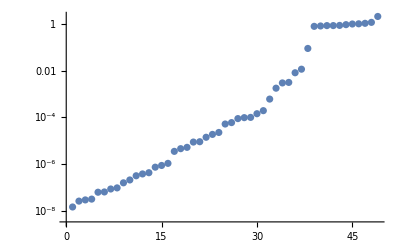

```mathematica
cdOGR[ng_]:=(mθ+=β(θ-mθ);mg+=β(ng-mg);m+=γ(ng-m); 
dθθ+=β((θ-mθ)^2-dθθ);dgg+=β((ng-mg)^2-dgg); 
θ-=η*m*Sqrt[dθθ/dgg]);  
β=0.4;γ=0.5;η=0.9;                         (* hyperparameters for cdOGR without cut *)

f=(1.5-x+x*y)^2+(2.25-x+x*y^2)^2+(2.625-x+x*y^3)^2; (* Beale function *)
m=mθ=mg=dθθ=dgg=Table[0,2];dθθ=dgg=Table[1,2];sub:={x->θ[[1]],y->θ[[2]]};
Table[ θ={sx,sy};Do[cdOGR[Grad[f,{x,y}]/.sub],{i,50}];
f/.sub,{sx,-3,3},{sy,-3,3}]//Flatten//Sort//ListLogPlot
```